## Cosmology — Problem Set 5 — Solution

### 1. Taylor-Wheeler-Bertschinger (TWB) Problem 3.1 on p. 3-35

A. Make estimates using Δσ=Δr/(1-2M/r)^(1/2).
M is in km so let’s convert that to M=5000m. The location of the event horizon is 2M=10000m.  For cases (a)-(e), the values in meters are 50000, 15000, 10100, 10010, and 10001, respectively. Δr is 1m in all cases.

```mathematica
Table[{r,N[1/(1-10000/r)^(1/2)]},{r,{50000,15000,10100,10010,10001}}]
```

{{50000,1.11803},{15000,1.73205},{10100,10.0499},{10010,31.6386},{10001,100.005}}

So at (a) r=50000m,  Δσ=1.12m, (b) r=15000m,  Δσ=1.73m, (c) r=10100m,  Δσ=10.05m, (d) r=10010m,  Δσ=31.63m, and (e) r=10001m,  Δσ=100.01m.

B. Make estimates using Eq. 18 on p. 3-16:

σ=z_H √(z_H^2-2M)+2M ln(z_H+√(z_H^2-2M))-z_L √(z_L^2-2M)+2M ln(z_L+√(z_L^2-2M))

where z_H=√r_H and z_L=√r_L and r_H=r_L+1. Everything is in meters and our answer will be in meters.

```mathematica
f[z_]:=z Sqrt[z^2-10000]+10000 Log[z+Sqrt[z^2-10000]]
```

```mathematica
Table[{r,N[f[Sqrt[r+1]]-f[Sqrt[r]]]},{r,{50000,15000,10100,10010,10001}}]
```

{{50000,1.11803},{15000,1.73199},{10100,10.0251},{10010,30.8856},{10001,82.8488}}

So at (a) r=50000m,  Δσ=1.12m, (b) r=15000m,  Δσ=1.73m, (c) r=10100m,  Δσ=10.03m, (d) r=10010m,  Δσ=30.89m, and (e) r=10001m,  Δσ=82.85m.

C. To three significant figures, (a), (b), and (c) agree. Then (d) is deviating even at two significant figures (32m vs 31m), and (e) is deviating even in the leading digit (100m vs. 83m).

If one wants an approximation that is good to much better than a fraction f (the authors are suggesting three significant figure accuracy, which is f=0.001), then

1/(1-10000/r_L)^(1/2)-1/(1-10000/(r_L+1))^(1/2) needs to be much less than f. If r_L=10000+d then the criterion for acceptable accuracy becomes:

1/(1-10000/(10000+d))^(1/2)-1/(1-10000/(10000+d+1))^(1/2)≪f

I am going to discuss the criterion and rearrange that to a statement about d in class, since it requires a bit of algebra and some good arguments that will be unlikely to rub off  if it is buried in a problem set solution.

Anybody who succeeds in pushing this through convincingly given your current experience level with approximations deserves some extra credit :)

### 2. TWB Problem 3.2 on p. 3-35

The statement the authors are asking you to verify is actually in Section 3.3 not 3.4.

The statement was: for a shell at 695980km and another shell at 695981km:

“the directly measured distance between the two would be not 1 kilometer, but 2 millimeters more than 1 kilometer.”

The hint was to use this approximation from inside the front cover:

(1+ϵ)^n≈1+nϵ

The authors want us to apply that to:

Δσ=Δr/(1-2M/r)^(1/2)

with n=-1/2 and ϵ=-(2M)/r.

So,

Δσ=(1+1/2(2M)/r)Δr=Δr+M/r Δr

So we have the 1km, that is the first time Δr. The additional 2mm in “2 millimeters more than 1 kilometer” must come from:
 
 M/r Δr=(1.45km)/(695980km)1km=1450000/695980 1mm=2.1mm

Exactly as claimed.

### 3. Inward Falling Light — Outside the Event Horizon

Eq. 26 on p. 3-25 is:

t-t_1=±(r-r_1+2M ln (r/M-2)/(r_1/M-2))

(a) If we put in t_1=0 and r_1=3M, the equation simplifies to:

t=±(r-3M+2M ln( r/M-2))

(b) There is a ± sign in your answer to Part (a). If the flashlight is directed inward then increasing t—which  since we started with t_1=0 means positive t—must correspond to decreasing r. So which sign is going to give you positive times for decreasing r? Simplify the formula to have just that sign.

We need the minus sign if decreasing r is going to correspond to increasing t:

t=-(r-3M+2M ln( r/M-2))

(c) Plug in r=2.5M to double-check:

t=-(2.5M-3M+2M ln( 2.5M/M-2))=-M(-0.5+2ln 0.5)=1.886M

(d)Take the equation t=-(r-3M+2M ln( r/M-2)) and divide both sides through by M:

t/M=-(r/M-3+2 ln( r/M-2))

Oh, isn’t that lovely. We see that if we think of t/M as a y-value and r/M as an x-value, then the equation is:

y=-(x-3+2ln(x-2))

and that is something we can graph!

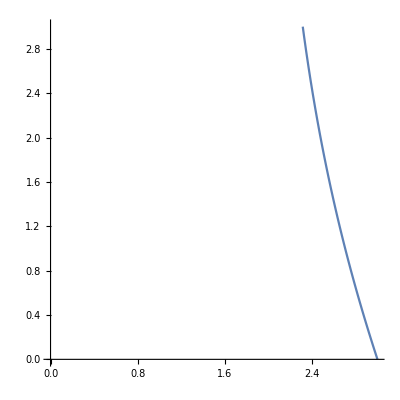

```mathematica
youtside[x_]:=-(x-3+2Log[x-2]);
Plot[youtside[x],{x,2,3}, PlotRange->{{0,3},{0,3}}, AspectRatio->1]
```

### 4. Inward Falling Light — Inside the Event Horizon

At r=2M is the event horizon, and our coordinates behave poorly there. So we will skip over that zone and use the same procedure again, but this time using t_1=0 and r_1=1.5M.

(a) If we put in t_1=0 and r_1=1.5M, the equation simplifies to:

t=±(r-1.5M+2M ln(r/M-2)/-0.5)=±(r-1.5M+2M ln(4-2r/M))

(b) Looks like we need the minus sign again:

t=-(r-1.5M+2M ln(4-2r/M))

(c) Plug in r=0.5M to double-check:

t=-(0.5M-1.5M+2M ln(4-2·0.5M/M))=-M(-1+2 ln3)=-1.197M

OOPS! I guess we needed the plus sign. Good thing we double-checked. The problem was that the 2ln3 overwhelmed the -1. So, for (b) we should have had:

t=r-1.5M+2M ln(4-2r/M)

and then for (c) we would have gotten

t=1.197M

(d) Same as 3(d), except the region to make the graph in will be 0<r/M<1.5.

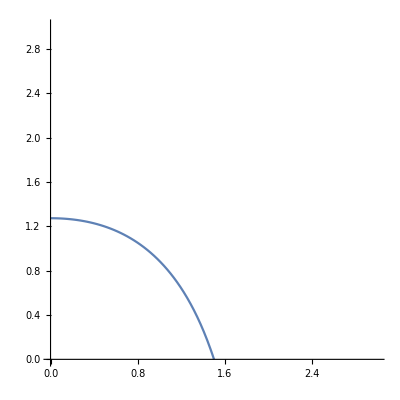

```mathematica
yinside[x_]:=x-1.5+2Log[4-2x];
Plot[yinside[x],{x,0,1.5}, PlotRange->{{0,3},{0,3}}, AspectRatio->1]
```

I want to see more of both graphs and pile them onto the same graph, so I can more readily compare with Fig. 8 on p. 3-24:

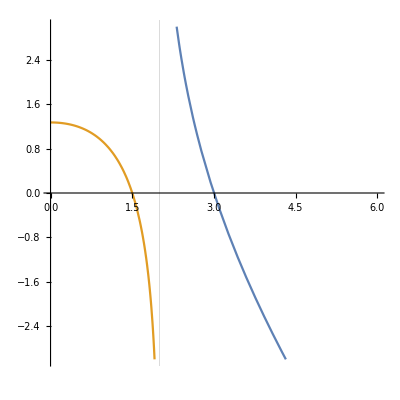

```mathematica
Plot[{youtside[x],yinside[x]},{x,0,8}, PlotRange->{{0,6},{-3,3}}, GridLines->{{2.0},{}}, AspectRatio->1]
```

### 5. TWB Problem 3.5 on p. 3-37

A. We need Δg/Δr. We had that on Problem 2-8(a) on Problem Set 1. The answer was:

Δg/Δr=-(2M)/r^3

The minus sign tells you that decreasing r is increasing g. In our study session, we said you might start to notice this when Δg is somewhere between 1 and 5% of Earth’s gravity. But our authors are suggesting you get uncomfortable (feeling like you might be torn apart) when Δg=g_E where g_E=-9.8m/s^2, the gravity at the surface of Earth. To make things rounder, let’s just take g_E=-10m/s^2.

So we have:

g_E/Δr=(-2M)/r_ouch^3

where Δr is the distance from your middle to your head. 

So r_ouch=((-2MΔr)/g_E)^(1/3)

B. Our authors say to take Δr=1m and to take M=10000m in the crazy units where mass is measured in meters (and they say that 10000m is about 7 times the mass of our Sun).

So we put all the numbers in:

r_ouch=((2·10000m ·1m)/(10m/s^2))^(1/3)

Oops, we have a problem. We need to convert the seconds to meters and the exact conversion factor is 299792458m=1s, which we can round to  3 10^8 m=1s.

r_ouch=((2000 m)/(1/(3 10^8 m)^2))^(1/3)=(18000/10^-16)^(1/3)m=(180 10^18 )^(1/3)m=5.6 10^6 m

Or, since our authors are also using km a lot, r_ouch=5600km.